To-do: Regular payoff distribution, rolling intrinsic payoff distribution. Show convergence.

Forward price evolution: dF_t=F_t σdW_t, or F_t=F_0 e^(-0.5 σ^2 t+σW_t)

```mathematica
F0=3.;
σ=0.3;
T=3.0/12; (*3 months*)
nsteps=90;
dt=T/nsteps; (*1 day per step*)
nmc=1000;
K=3.2;
```

```mathematica
Wt=FoldList[Plus,0.0Range[nmc],√dt RandomVariate[NormalDistribution[0,1],{nsteps,nmc}]]//Rest;
```

```mathematica
Mean[Wt_[[-1]]]
```

0.0114303

```mathematica
StandardDeviation[Wt_[[-1]]]
```

0.492798

```mathematica
Ft=F0 Exp[-0.5 σ^2 dt Range[nsteps]+σ Wt];
```

```mathematica
Mean[Ft_[[-1]]]
```

3.0094

```mathematica
payoff[F_]:=Max[F-K,0];
SetAttributes[payoff,Listable];
```

```mathematica
policy[F_]:=If[F>K,1,0];
SetAttributes[policy,Listable];
```

```mathematica
Mean[payoff[Ft_[[-1]]]]
```

0.105027

```mathematica
FinancialDerivative[{"Future","European","Call"},{"StrikePrice"->K,"Expiration"->T},{"CurrentPrice"->F0,"Volatility"->σ,"InterestRate"->0}]
```

0.10219

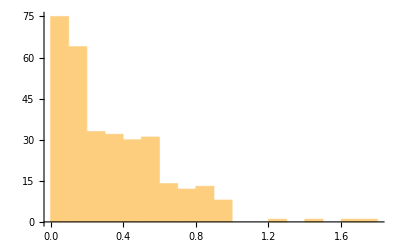

```mathematica
Histogram[Select[payoff[Ft_[[-1]]],Positive]]
```

How do I code rolling intrinsic?
Take a path

```mathematica
pps=policy[Ft];
```

```mathematica
pps_[[All,1]]
```

{0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}